```mathematica
D[1/b[η],{η,2}]/(1/b[η])==D[1/a[η],{η,2}]/(1/a[η])+k
%/.{a->Function[η,√Sinh[2η]], k->-1}//FullSimplify
%/.{b->Function[η,1/y[η]]}//FullSimplify
Inactive[DSolve][%,y,η]
DSolveChangeVariables[%,y,z,z==Sinh[2 η]^2]//FullSimplify
Activate[%]
```

b[η] ((2 b'[η]^2)/b[η]^3-b''[η]/b[η]^2)==k+a[η] ((2 a'[η]^2)/a[η]^3-a''[η]/a[η]^2)

3 b[η] Csch[2 η]^2+b''[η]==(2 b'[η]^2)/b[η]

3 Csch[2 η]^2==y''[η]/y[η]

DSolve[3 Csch[2 η]^2==y''[η]/y[η],y,η]

DSolve[(8 ((1+2 z) y'[z]+2 z (1+z) y''[z]))/y[z]==3/z,y,z]

{{y→Function[{z},z^(3/4) C[1] Hypergeometric2F1[3/4,3/4,2,-z]+C[2] MeijerG[{{},{1,1}},{{-1/4,3/4},{}},-z]]}}

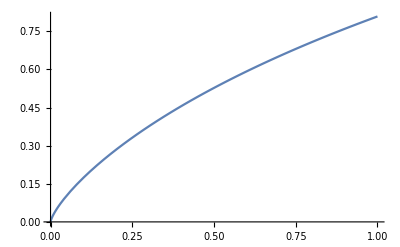

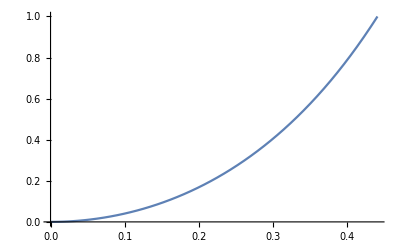

```mathematica
Plot[{z^(3/4) Hypergeometric2F1[3/4,3/4,2,-z]},{z,0,1}]
Plot[Sinh[2η]^2,{η,0,0.5*ArcSinh[1]}]
```

```mathematica
$Assumptions={0<z,z<1,0<η,η<0.5*ArcSinh[1]};
z^(3/4) Hypergeometric2F1[3/4,3/4,2,-z]//FunctionExpand//FullSimplify
%/.{z->Sinh[2η]^2}//FullSimplify
```

1/(π z^(1/4))8 √2 √(1+√(1+z)) (-EllipticE[(2+z-2 √(1+z))/z]+EllipticK[(2+z-2 √(1+z))/z])

(16 Cosh[η] (-EllipticE[Tanh[η]^2]+EllipticK[Tanh[η]^2]))/(π √Sinh[2 η])

```mathematica
MeijerG[{{},{1,1}},{{-1/4,3/4},{}},-z]//FunctionExpand//FullSimplify
%/.{z->Sinh[2η]^2}//FullSimplify
```

1/(π^2 (-z)^(1/4))4 (-2 EllipticE[1/2 (1-√(1+z))]+2 EllipticE[1/2 (1+√(1+z))]+(1+√(1+z)) EllipticK[1/2 (1-√(1+z))]+(-1+√(1+z)) EllipticK[1/2 (1+√(1+z))]) Gamma[3/4]^2

(8 Gamma[3/4]^2 (EllipticE[Cosh[η]^2]-EllipticE[-Sinh[η]^2]+Cosh[η]^2 EllipticK[-Sinh[η]^2]+EllipticK[Cosh[η]^2] Sinh[η]^2))/(π^2 (-Sinh[2 η]^2)^(1/4))

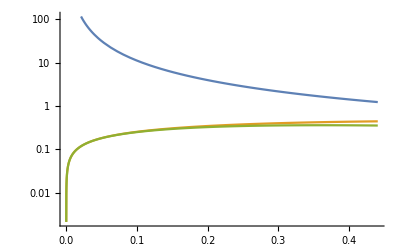

```mathematica
LogPlot[{1/((16 Cosh[η] (-EllipticE[Tanh[η]^2]+EllipticK[Tanh[η]^2]))/(π √Sinh[2 η])),Im[1/(1/(π^2 (-Sinh[2 η]^2)^(1/4))8 Gamma[3/4]^2 (EllipticE[Cosh[η]^2]-EllipticE[-Sinh[η]^2]+Cosh[η]^2 EllipticK[-Sinh[η]^2]+EllipticK[Cosh[η]^2] Sinh[η]^2))],Re[1/(1/(π^2 (-Sinh[2 η]^2)^(1/4))8 Gamma[3/4]^2 (EllipticE[Cosh[η]^2]-EllipticE[-Sinh[η]^2]+Cosh[η]^2 EllipticK[-Sinh[η]^2]+EllipticK[Cosh[η]^2] Sinh[η]^2))]},{η,0,ArcSinh[1]/2}]
```

```mathematica
Show[LogPlot[{1/((16 Cosh[η] (-EllipticE[Tanh[η]^2]+EllipticK[Tanh[η]^2]))/(π √Sinh[2 η])),Im[1/(1/(π^2 (-Sinh[2 η]^2)^(1/4))8 Gamma[3/4]^2 (EllipticE[Cosh[η]^2]-EllipticE[-Sinh[η]^2]+Cosh[η]^2 EllipticK[-Sinh[η]^2]+EllipticK[Cosh[η]^2] Sinh[η]^2))],Re[1/(1/(π^2 (-Sinh[2 η]^2)^(1/4))8 Gamma[3/4]^2 (EllipticE[Cosh[η]^2]-EllipticE[-Sinh[η]^2]+Cosh[η]^2 EllipticK[-Sinh[η]^2]+EllipticK[Cosh[η]^2] Sinh[η]^2))]},{η,0,ArcSinh[1]/2}, PlotRange->{{-0.001,0.4},{0.005,500}},ImageSize->500, AspectRatio->2/3,Frame->True,Axes->False,FrameStyle->Directive[Black,Thickness[0.0025], FontSize->20], FrameLabel->{Style["η", FontSize->32,FontFamily->"Times"],Style["f(η)",FontSize->24,FontFamily->"Times"]},PlotLegends->Placed[LineLegend[{Text[Style[ToExpression["_2F_1",TeXForm,HoldForm]]],Text[Style[ToExpression["\Im{G^{2.0}_{2.2}}",TeXForm,HoldForm]]],Text[Style[ToExpression["\Re{G^{2.0}_{2.2}}",TeXForm,HoldForm]]]}, LabelStyle->Directive[FontSize->16],LegendFunction->(Framed[#1, FrameMargins->5,RoundingRadius->8,FrameStyle->Gray]&)],Scaled[{.275,.825}]]
]]
```

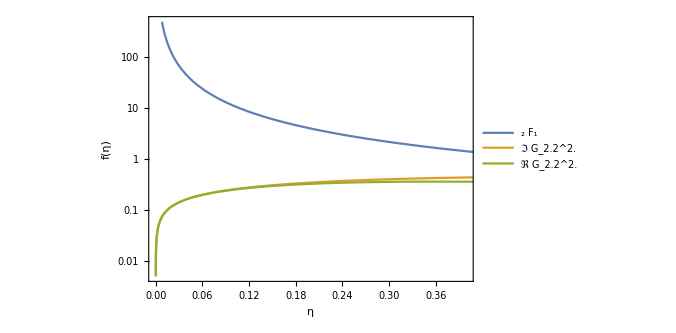

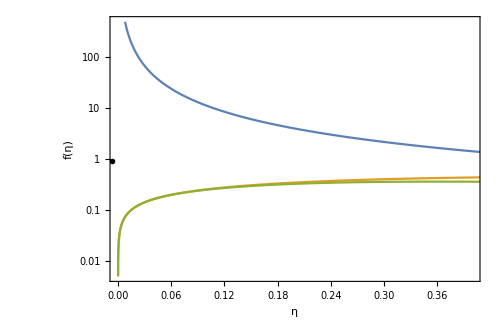

```mathematica
Series[1/(A(16 Cosh[η] (-EllipticE[Tanh[η]^2]+EllipticK[Tanh[η]^2]))/(π √Sinh[2 η])+B(1/(π^2 (-Sinh[2 η]^2)^(1/4))8 Gamma[3/4]^2 (EllipticE[Cosh[η]^2]-EllipticE[-Sinh[η]^2]+Cosh[η]^2 EllipticK[-Sinh[η]^2]+EllipticK[Cosh[η]^2] Sinh[η]^2))), {η,0,3}]//FunctionExpand//FullSimplify
```

((2+2 ⅈ) π^2 √η)/(B Gamma[-1/4]^2)-((8/3+(8 ⅈ)/3) π^2 (6 (-1)^(1/4) A π^2-B Gamma[3/4]^2+(3-3 ⅈ) B π Gamma[3/4]^2+12 B Gamma[3/4]^2 Log[2]-6 B Gamma[3/4]^2 Log[η]) η^(5/2))/(B^2 Gamma[-1/4]^4)+O[η]^(7/2)

```mathematica
Manipulate[Plot[{Re[((2+2 ⅈ) π^2 √η)/(B Gamma[-1/4]^2)-1/(B^2 Gamma[-1/4]^4)(8/3+(8 ⅈ)/3) π^2 (6 (-1)^(1/4) A π^2-B Gamma[3/4]^2+(3-3 ⅈ) B π Gamma[3/4]^2+12 B Gamma[3/4]^2 Log[2]-6 B Gamma[3/4]^2 Log[η]) η^(5/2)], √Sinh[2η]},{η,0,0.5ArcSinh[1]}],{{A,1},-1,5},{{B,1},-1,5}]
```

```mathematica
((2+2 ⅈ) π^2 √η)/(B Gamma[-1/4]^2)-1/(B^2 Gamma[-1/4]^4)(8/3+(8 ⅈ)/3) π^2 (6 (-1)^(1/4) A π^2-B Gamma[3/4]^2+(3-3 ⅈ) B π Gamma[3/4]^2+12 B Gamma[3/4]^2 Log[2]-6 B Gamma[3/4]^2 Log[η]) η^(5/2)
D[%,η]
Solve[Limit[Re[%]/(√Sinh[2η]),η->0]==1,B]
```

((2+2 ⅈ) π^2 √η)/(B Gamma[-1/4]^2)-((8/3+(8 ⅈ)/3) π^2 η^(5/2) (6 (-1)^(1/4) A π^2-B Gamma[3/4]^2+(3-3 ⅈ) B π Gamma[3/4]^2+12 B Gamma[3/4]^2 Log[2]-6 B Gamma[3/4]^2 Log[η]))/(B^2 Gamma[-1/4]^4)

((1+ⅈ) π^2)/(B √η Gamma[-1/4]^2)+((16+16 ⅈ) π^2 η^(3/2) Gamma[3/4]^2)/(B Gamma[-1/4]^4)-1/(B^2 Gamma[-1/4]^4)(20/3+(20 ⅈ)/3) π^2 η^(3/2) (6 (-1)^(1/4) A π^2-B Gamma[3/4]^2+(3-3 ⅈ) B π Gamma[3/4]^2+12 B Gamma[3/4]^2 Log[2]-6 B Gamma[3/4]^2 Log[η])

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

{}

((1+ⅈ) π^2)/(B √η Gamma[-1/4]^2)+((16+16 ⅈ) π^2 η^(3/2) Gamma[3/4]^2)/(B Gamma[-1/4]^4)-1/(B^2 Gamma[-1/4]^4)(20/3+(20 ⅈ)/3) π^2 η^(3/2) (6 (-1)^(1/4) A π^2-B Gamma[3/4]^2+(3-3 ⅈ) B π Gamma[3/4]^2+12 B Gamma[3/4]^2 Log[2]-6 B Gamma[3/4]^2 Log[η])

((1+ⅈ) π^2)/(√η Gamma[-1/4]^2)+((16+16 ⅈ) π^2 η^(3/2) Gamma[3/4]^2)/Gamma[-1/4]^4-((20/3+(20 ⅈ)/3) π^2 η^(3/2) (6 (-1)^(1/4) π^2-Gamma[3/4]^2+(3-3 ⅈ) π Gamma[3/4]^2+12 Gamma[3/4]^2 Log[2]-6 Gamma[3/4]^2 Log[η]))/Gamma[-1/4]^4

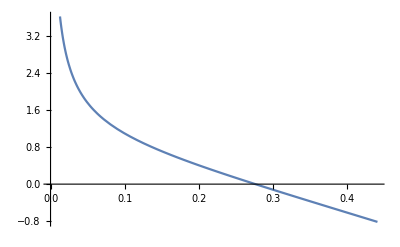

```mathematica
((1+ⅈ) π^2)/(B √η Gamma[-1/4]^2)+((16+16 ⅈ) π^2 η^(3/2) Gamma[3/4]^2)/(B Gamma[-1/4]^4)-1/(B^2 Gamma[-1/4]^4)(20/3+(20 ⅈ)/3) π^2 η^(3/2) (6 (-1)^(1/4) A π^2-B Gamma[3/4]^2+(3-3 ⅈ) B π Gamma[3/4]^2+12 B Gamma[3/4]^2 Log[2]-6 B Gamma[3/4]^2 Log[η])
%/.{A->1,B->1}
Plot[Re[%],{η,0,0.5*ArcSinh[1]}]
```